# 1 Loop Processes

## Introduction

This notebook is designed to automate the calculation of 1 loop  processes. We will split the operators into two types for these calculations:
	1. [
	2. [
Computing these 1 loop integrals will involve evaluating the time ordered product

Where, here,  and  are the Wilson operators and coefficients, respectively. There is no implicit sum, instead we shall evaluate the integral for each of our operators
There are 10 operators we shall consider, these operators have been created to avoid tracing over matrices in d dimensions. They are
                 ✓
                           ✓
                                 ✓
                      ✓
                          ✓
               ✓
                            ✓
                  ✓
                      ✓
         ✓
Note that in the original basis  terms are instead  and  terms are instead  where  is the charge of the quark. Unlike in our basis, in this basis  and  will not share a linear relation.
We shall keep the Wilson coefficients general
Note that  is a short hand for ;   is the standard su(3) colour operator and  as usual

## Import files

We will use Package-X for these calculations, note that the primer for this can be found at primer

```mathematica
<<X`
```

Package-X v2.1.1 [patched 22/08/2020], by Hiren H. Patel
For more information, see the

Some quick notes on Package-X:
	1. Esc g Esc gives gamma matrix
	2. Esc gg Esc gives metric
	3. Ecs 11 Esc gives identity matrix
	4. ctrl underscore lets you place indices
	5. Trace is denoted with Spur and each element is separated by a comma
	6. Arguments of LoopIntegrate are [numerator, {p,m0},{p-k,m1}] , where {p,m0} denotes a term of the form  in denominator, this gives a d dimensional integral

## Calculations

In order to perform these calculations we first take the general form of the operator and wicks contract. We will then Fourier transform to momentum space. Having done this, the calculation proceeds as usual. For explicit working of these initial steps refer to my Progression review document
One last thing to consider is how to deal with the operators with a  type structure in them. We recall the Fierz identity,
.
For the case of  we will have the structure  since the  quarks have the same colour (they are linked by a QED vertex). We note that 

We can, therefore, take this out as a prefactor
In the case of  ,  and the operators that depend on them, we can take thes out, as before. This time the colour structure is  as the  quarks are now a closed loop. This gives us the trace of . We can now see that all these operators will give us 0.

### Type 1 operator

The general form of the integral (i.e. using and ) is


We can now use Package-X to perform the integral. We will leave the  term out and manually add the  and  when writing our results.

```mathematica
loopO1 = deltaIJ CF loopO2
```

CF deltaIJ loopO2

```mathematica
Gamma1op2 =DiracMatrix[ Subscript[γ, ν],ℙL]
Gamma2op2 = DiracMatrix[ Subscript[γ, ν],ℙL]
```

DiracMatrix[γ_ν,ℙL]

DiracMatrix[γ_ν,ℙL]

```mathematica
num2 =FermionLineExpand[Contract[DiracMatrix[-Gamma1op2,(l.γ+mc 𝟙),Subscript[γ, μ],(l.γ+q.γ+mc 𝟙),Gamma2op2]]]
```

(6-𝒹) DiracMatrix[γ_μ,γ.l,γ.q,ℙL]+DiracMatrix[γ_μ,ℙL] (-2 mc^2+𝒹 mc^2+2 l.l-𝒹 l.l-4 l.q)+(-4+2 𝒹) DiracMatrix[γ.l,ℙL] l_μ+(-8+2 𝒹) DiracMatrix[γ.q,ℙL] l_μ+4 DiracMatrix[γ.l,ℙL] q_μ

```mathematica
loopO2test  = LoopIntegrate[num2,l,{l,mc},{l+q,mc}]
```

DiracMatrix[γ.q,ℙL] q_μ (-4 PVB[0,1,q.q,mc,mc]+2 𝒹 PVB[0,1,q.q,mc,mc]-4 PVB[0,2,q.q,mc,mc]+2 𝒹 PVB[0,2,q.q,mc,mc])+DiracMatrix[γ_μ,ℙL] (2 PVA[0,mc]-𝒹 PVA[0,mc]+2 q.q PVB[0,0,q.q,mc,mc]+q.q (6 PVB[0,1,q.q,mc,mc]-𝒹 PVB[0,1,q.q,mc,mc])-4 PVB[1,0,q.q,mc,mc]+2 𝒹 PVB[1,0,q.q,mc,mc])

```mathematica
loopO2 = Simplify[LoopRefine[loopO2test]]
```

(2 (12 mc^2+3 DiscB[q.q,mc,mc] (2 mc^2+q.q)+q.q (2+3/ϵ+3 Log[µ^2/mc^2])) (DiracMatrix[γ_μ,ℙL] q.q-DiracMatrix[γ.q,ℙL] q_μ))/(9 q.q)

### Type 2 operator

The general form of the integral is

We can now use Package-X to perform the integral. Note that this calculation will explicitly not include the  factor, which we will have to manually add when we write out the result. We’ve also left the  term out

```mathematica
Gamma1op3 = DiracMatrix[Subscript[γ, ν],ℙL]
Gamma2op3 =Subscript[γ, ν]
```

DiracMatrix[γ_ν,ℙL]

γ_ν

```mathematica
num3 =Contract[- Spur[(l.γ+mc 𝟙),Subscript[γ, μ],((l-q).γ+mc 𝟙),Gamma2op3]]
```

-8 l_μ l_ν+4 l_ν q_μ+4 l_μ q_ν-4 mc^2 𝕘_(μ,ν)+4 (l.l-l.q) 𝕘_(μ,ν)

```mathematica
loopO3test  = LoopIntegrate[num3,l,{l,mc},{l-q,mc}]
```

q_μ q_ν (-8 PVB[0,1,q.q,mc,mc]-8 PVB[0,2,q.q,mc,mc])+𝕘_(μ,ν) (4 PVA[0,mc]-2 q.q PVB[0,0,q.q,mc,mc]-8 PVB[1,0,q.q,mc,mc])

```mathematica
loopO3=Simplify[LoopRefine[loopO3test]]
```

(4 (12 mc^2+3 DiscB[q.q,mc,mc] (2 mc^2+q.q)+q.q (5+3/ϵ+3 Log[µ^2/mc^2])) (q_μ q_ν-q.q 𝕘_(μ,ν)))/(9 q.q)

```mathematica
loopO4= 0
```

0

```mathematica
Gamm1op5 = DiracMatrix[Subscript[γ, ν],Subscript[γ, ρ],Subscript[γ, κ],ℙL]
Gamma2op5 =DiracMatrix[Subscript[γ, ν],Subscript[γ, ρ],Subscript[γ, κ]]
```

DiracMatrix[γ_ν,γ_ρ,γ_κ,ℙL]

DiracMatrix[γ_ν,γ_ρ,γ_κ]

```mathematica
num5 =Contract[Spur[-(l.γ+mc 𝟙),Subscript[γ, μ],((l+q).γ+mc 𝟙),Gamma2op5]]
```

4 l_ρ q_ν 𝕘_(κ,μ)-4 l_ν q_ρ 𝕘_(κ,μ)+8 l_μ l_ρ 𝕘_(κ,ν)+4 l_ρ q_μ 𝕘_(κ,ν)+4 l_μ q_ρ 𝕘_(κ,ν)-8 l_μ l_ν 𝕘_(κ,ρ)-4 l_ν q_μ 𝕘_(κ,ρ)-4 l_μ q_ν 𝕘_(κ,ρ)-4 l_ρ q_κ 𝕘_(μ,ν)+4 l_κ q_ρ 𝕘_(μ,ν)-4 mc^2 𝕘_(κ,ρ) 𝕘_(μ,ν)+4 (l.l+l.q) 𝕘_(κ,ρ) 𝕘_(μ,ν)+4 l_ν q_κ 𝕘_(μ,ρ)-4 l_κ q_ν 𝕘_(μ,ρ)+4 mc^2 𝕘_(κ,ν) 𝕘_(μ,ρ)-4 (l.l+l.q) 𝕘_(κ,ν) 𝕘_(μ,ρ)-8 l_κ l_μ 𝕘_(ν,ρ)-4 l_μ q_κ 𝕘_(ν,ρ)-4 l_κ q_μ 𝕘_(ν,ρ)-4 mc^2 𝕘_(κ,μ) 𝕘_(ν,ρ)+4 (l.l+l.q) 𝕘_(κ,μ) 𝕘_(ν,ρ)

```mathematica
loopO5test  = LoopIntegrate[num5,l,{l,mc},{l+q,mc}]
```

q_μ q_ν 𝕘_(κ,ρ) (-8 PVB[0,1,q.q,mc,mc]-8 PVB[0,2,q.q,mc,mc])+q_κ q_μ 𝕘_(ν,ρ) (-8 PVB[0,1,q.q,mc,mc]-8 PVB[0,2,q.q,mc,mc])+q_μ q_ρ 𝕘_(κ,ν) (8 PVB[0,1,q.q,mc,mc]+8 PVB[0,2,q.q,mc,mc])+𝕘_(κ,ρ) 𝕘_(μ,ν) (4 PVA[0,mc]-2 q.q PVB[0,0,q.q,mc,mc]-8 PVB[1,0,q.q,mc,mc])+𝕘_(κ,μ) 𝕘_(ν,ρ) (4 PVA[0,mc]-2 q.q PVB[0,0,q.q,mc,mc]-8 PVB[1,0,q.q,mc,mc])+𝕘_(κ,ν) 𝕘_(μ,ρ) (-4 PVA[0,mc]+2 q.q PVB[0,0,q.q,mc,mc]+8 PVB[1,0,q.q,mc,mc])

```mathematica
loopO5= Simplify[LoopRefine[loopO2test]]
```

(2 (12 mc^2+3 DiscB[q.q,mc,mc] (2 mc^2+q.q)+q.q (2+3/ϵ+3 Log[µ^2/mc^2])) (DiracMatrix[γ_μ,ℙL] q.q-DiracMatrix[γ.q,ℙL] q_μ))/(9 q.q)

```mathematica
loopO6 = 0
```

0

```mathematica
loopO7=2/3loopO3
```

(8 (12 mc^2+3 DiscB[q.q,mc,mc] (2 mc^2+q.q)+q.q (5+3/ϵ+3 Log[µ^2/mc^2])) (q_μ q_ν-q.q 𝕘_(μ,ν)))/(27 q.q)

```mathematica
loopO8=2/3loopO4
```

0

```mathematica
loopO9=2/3 loopO5
```

(4 (12 mc^2+3 DiscB[q.q,mc,mc] (2 mc^2+q.q)+q.q (2+3/ϵ+3 Log[µ^2/mc^2])) (DiracMatrix[γ_μ,ℙL] q.q-DiracMatrix[γ.q,ℙL] q_μ))/(27 q.q)

```mathematica
loopO10=2/3loopO6
```

0

## Summary

We have now performed all our 1 loop calculations. We have seen that there are, in fact, only 3 linearly independent non-zero contributions. These are from  and . 
;  and 
All other operators gives us vanishing results for the 1 loop calculations
We also currently have

```mathematica
loopO2-loopO5
```

0

```mathematica
DiscExpand[DiscB[q.q,mc,mc] ]
```

(√(q.q (-4 mc^2+q.q)) Log[(2 mc^2-q.q+√(q.q (-4 mc^2+q.q)))/(2 mc^2)])/(q.q)

## Passarino-Veltman Comparison for

```mathematica
LoopRefine[PVA[1,mc]]
```

(3 mc^4)/8+1/4 mc^4 (1/ϵ+Log[µ^2/mc^2])

```mathematica
typeA[r_]:= Simplify[Series[(4 Pi μ^2)^ϵ(4Pi Exp[-EulerGamma])^-ϵ(-1)^(1+r)/2^r Gamma[ϵ-1-r] (mc2)^(1-ϵ+r),{ϵ,0,0}]]
```

```mathematica
typeA[1]
```

mc2^2/(4 ϵ)+1/8 mc2^2 (3-2 Log[mc2]+2 Log[μ^2])+O[ϵ]^1

```mathematica
Subscript[q, μ] Subscript[q, ν] (-8 PVB[0,1,q.q,mc,mc]-8 PVB[0,2,q.q,mc,mc])+Subscript[𝕘, μ,ν] (4 PVA[0,mc]-2 q.q PVB[0,0,q.q,mc,mc]-8 PVB[1,0,q.q,mc,mc])
```

```mathematica
Simplify[ q.q LoopRefine[(8 PVB[0,1,q.q,mc,mc]+8 PVB[0,2,q.q,mc,mc])]]/Simplify[LoopRefine[4 PVA[0,mc]-2 q.q PVB[0,0,q.q,mc,mc]-8 PVB[1,0,q.q,mc,mc]]]
```

1

```mathematica
Simplify[8(Subscript[q, μ] Subscript[q, ν]-q.q Subscript[𝕘, μ,ν] )LoopRefine[( PVB[0,1,q.q,mc,mc]+ PVB[0,2,q.q,mc,mc])]-(-LoopRefine[(Subscript[q, μ] Subscript[q, ν] (-8 PVB[0,1,q.q,mc,mc]-8 PVB[0,2,q.q,mc,mc])+Subscript[𝕘, μ,ν] (4 PVA[0,mc]-2 q.q PVB[0,0,q.q,mc,mc]-8 PVB[1,0,q.q,mc,mc]))])]
```

0

## Comparison using prescription for

```mathematica
directCalc =Simplify[Collect[8/ϵ Integrate[x(1-x)(1-ϵ Log[Re[m2]-q2 (1-x) x] ),{x,0,1},Assumptions->{Re[m2]>0},GenerateConditions->False]+4/3 Log[μ2],ϵ]]/.Re[m2]->m2
```

4/9 (5+3/ϵ-6 √(1-(4 m2)/q2) ArcCoth[√(1-(4 m2)/q2)]+(12 m2 (√q2-√(-4 m2+q2) ArcCoth[√(1-(4 m2)/q2)]))/q2^(3/2)-3 Log[m2]+3 Log[μ2])

```mathematica
TeXForm[directCalc/.μ2->1]
```

\frac{4}{9} \left(\frac{12 \text{m2} \left(\sqrt{\text{q2}}-\sqrt{\text{q2}-4 \text{m2}} \coth ^{-1}\left(\sqrt{1-\frac{4
   \text{m2}}{\text{q2}}}\right)\right)}{\text{q2}^{3/2}}-6 \sqrt{1-\frac{4 \text{m2}}{\text{q2}}} \coth ^{-1}\left(\sqrt{1-\frac{4
   \text{m2}}{\text{q2}}}\right)-3 \log (\text{m2})+\frac{3}{\epsilon }+5\right)

Numerically evaluate both this and package-X for negative q2 with  prescription

```mathematica
DiscExpand[loopO3]/. q.q ->q2
```

(4 (12 mc^2+q2 (5+3/ϵ+3 Log[µ^2/mc^2])+(3 √(q2 (-4 mc^2+q2)) (2 mc^2+q2) Log[(2 mc^2-q2+√(q2 (-4 mc^2+q2)))/(2 mc^2)])/q2) (q_μ q_ν-q2 𝕘_(μ,ν)))/(9 q2)

```mathematica
packageXcalc= FullSimplify[(4 (12 mc^2+q2 (5+3/ϵ+3 Log[µ^2/mc^2])+(3 √(q2 (-4 mc^2+q2)) (2 mc^2+q2) Log[(2 mc^2-q2+√(q2 (-4 mc^2+q2)))/(2 mc^2)])/q2))/(9 q2)/.{Log[µ^2/mc^2]->Log[μ^2]-Log[mc^2],Log[(2 mc^2-q2+√(q2 (-4 mc^2+q2)))/(2 mc^2)]->Log[2 mc^2-q2+√(q2 (-4 mc^2+q2))]-Log[2 mc^2]}/.{mc^2->m2,μ^2->1}]
```

(4 (12 m2+q2 (5+3/ϵ-3 Log[m2])+(3 √(q2 (-4 m2+q2)) (2 m2+q2) (-Log[2 m2]+Log[2 m2-q2+√(q2 (-4 m2+q2))]))/q2))/(9 q2)

```mathematica
TeXForm[packageXcalc]
```

\frac{4 \left(\text{q2} \left(-3 \log (\text{m2})+\frac{3}{\epsilon }+5\right)+\frac{3 \sqrt{\text{q2} (\text{q2}-4 \text{m2})} (2
   \text{m2}+\text{q2}) \left(\log \left(\sqrt{\text{q2} (\text{q2}-4 \text{m2})}+2 \text{m2}-\text{q2}\right)-\log (2
   \text{m2})\right)}{\text{q2}}+12 \text{m2}\right)}{9 \text{q2}}

```mathematica
directCalc1=directCalc/.{μ2->1,m2->1.27^2}
```

4/9 (3.5659+3/ϵ-6 √(1-6.4516/q2) ArcCoth[√(1-6.4516/q2)]+(19.3548 (√q2-√(-6.4516+q2) ArcCoth[√(1-6.4516/q2)]))/q2^(3/2))

```mathematica
packageXcalc1=packageXcalc/.{μ->1,m2->1.27^2}
```

(4 (19.3548+q2 (3.5659+3/ϵ)+(3 √((-6.4516+q2) q2) (3.2258+q2) (-1.17118+Log[3.2258-q2+√((-6.4516+q2) q2)]))/q2))/(9 q2)

```mathematica
diff=FullSimplify[FullSimplify[directCalc1/.q2->q2+0.0001ⅈ]-FullSimplify[(packageXcalc1 /.q2->q2+0.0001 ⅈ)]]
```

(-(8.60213 √((-6.4516+0.0001 ⅈ)+q2))/((0.+0.0001 ⅈ)+q2)^(3/2)-8/3 √(1-6.4516/((0.+0.0001 ⅈ)+q2))) ArcCoth[√(1-6.4516/((0.+0.0001 ⅈ)+q2))]-1/((0.+0.0001 ⅈ)+q2)^2 1.33333 √(((-6.4516+0.0001 ⅈ)+q2) ((0.+0.0001 ⅈ)+q2)) ((3.2258+0.0001 ⅈ)+q2) (-1.17118+Log[(3.2258-0.0001 ⅈ)-q2+√(((-6.4516+0.0001 ⅈ)+q2) ((0.+0.0001 ⅈ)+q2))])

```mathematica
FullSimplify[packageXcalc1/. q2->-2]
```

-0.930794+1.33333/ϵ

```mathematica
FullSimplify[(directCalc1/.q2->-2)]
```

directCalc1

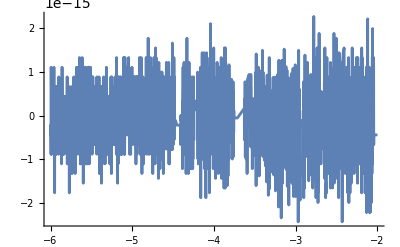

```mathematica
Plot[Re[diff],{q2,-6,-2}]
```

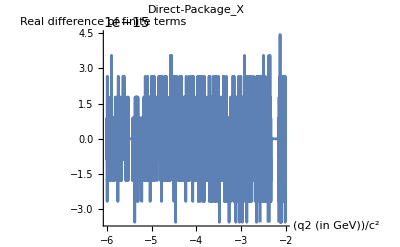

```mathematica
Show[%22,AxesLabel->{HoldForm[(q2 (in GeV))/c^2],HoldForm[Real difference of finite terms]},PlotLabel->HoldForm[Direct-Package_X],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\eryka\\Desktop\\Ery\\PhD\\Project work\\real_difference_of_finite_terms.png",%24,"PNG"]
```

C:\Users\eryka\Desktop\Ery\PhD\Project work\real_difference_of_finite_terms.png

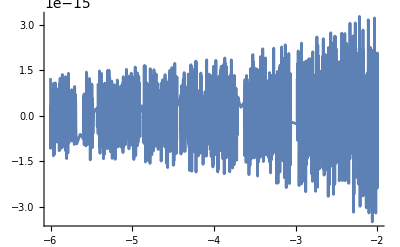

```mathematica
Plot[Im[diff],{q2,-6,-2}]
```

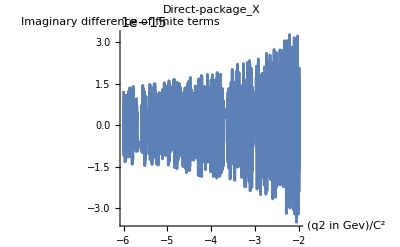

```mathematica
Show[%26,AxesLabel->{HoldForm[(q2 in Gev)/C^2],HoldForm[Imaginary difference of finite terms]},PlotLabel->HoldForm[Direct-package_X],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\eryka\\Desktop\\Ery\\PhD\\Project work\\imaginary_difference_of_finite_terms.png",%27,"PNG"]
```

C:\Users\eryka\Desktop\Ery\PhD\Project work\imaginary_difference_of_finite_terms.png

```mathematica
rat=FullSimplify[Series[Collect[FullSimplify[FullSimplify[(directCalc1/.q2->q2+ⅈ 0.0001)]/FullSimplify[(packageXcalc1/. q2->q2+ⅈ 0.0001)]],ϵ],{ϵ,0,1}]]
```

1.+((-(6.4516 √((-6.4516+0.0001 ⅈ)+q2))/((0.+0.0001 ⅈ)+q2)^(3/2)-2. √(1-6.4516/((0.+0.0001 ⅈ)+q2))) ArcCoth[√(1-6.4516/((0.+0.0001 ⅈ)+q2))]-1/((0.+0.0001 ⅈ)+q2)^2 1. √(((-6.4516+0.0001 ⅈ)+q2) ((0.+0.0001 ⅈ)+q2)) ((3.2258+0.0001 ⅈ)+q2) (-1.17118+Log[(3.2258-0.0001 ⅈ)-q2+√(((-6.4516+0.0001 ⅈ)+q2) ((0.+0.0001 ⅈ)+q2))])) ϵ+O[ϵ]^2

```mathematica
Plot[Re[rat],{q2,-6,-2}]
```

-Graphics-

```mathematica
diff/.q2->-2.74
```

1.55431×10^-15-1.42434×10^-15 ⅈ